ADDITIVE LOGISTIC PROCESSES. SOME CODE

Author: Lorenzo Torricelli.  lorenzo.torricelli@unipr.it
Code can be freely used and modified, but it comes with no guarantee on its accuracy

Reference. P. Carr and L. Torricelli "Additive logisitc processes in option pricing" 2021. Retrivable at SSRN https://papers.ssrn.com/sol3/papers.cfm?abstract_id=3647466

This notebook implements some formulae in the paper Carr and Torricelli 2021 and produces visual outputs. 
CPDA : conjugate - power Dagum additive model. Positive martingale pricing model of additive type (Markov with inhomeogeneous dependent increments) price whose log-returns are leptokurtic and skewed (skew-logistic distribution). 
SSLA : self - similar logistic additive model. Real-valued symmetric martingale pricing  model of additive type with centered returns and leptokurtosis.

The models produce closed formula for vanilla prices, PDFs, CDFs, tractable expressions for exotic derviatives, flexible volatility smile/skew and term sturcture, with a parsimonious parametrization.  Both models are pure jump.

Term functions for the CPDA and SSLA models.  Section 5 Carr and Torricelli.
  t : time to maturity
sigma : "volatility"
H : "self-similarity" parameter

```mathematica
b[t_, sigma_,  H_]:=(1-Exp[- t sigma ^(1/H)])^(H)
```

```mathematica
s[t_, sigma_, H_]:=sigma t^H
```

Option Prices.  Section 2 Carr and Torricelli
t : time to maturity
K : strike price
S : spot price

```mathematica
CPDAPut[K_, S_, t_, sigma_,H_]:=(K^(1/b[t, sigma,  H])+S^(1/b[t, sigma,  H] ))^b[t, sigma,  H]-S
SSLAPut[K_, S_, t_, sigma_,H_]:=s[t, sigma, H] Log[1+Exp[-(S-K)/ s[t, sigma, H] ]]
CPDACall[K_, S_, t_, sigma_,H_]:=(K^(1/b[t, sigma,  H])+S^(1/b[t, sigma,  H] ))^b[t, sigma,  H]-K
SSLACall[K_, S_, t_, sigma_,H_]:=s[t, sigma, H] Log[1+Exp[(S-K)/ s[t, sigma, H] ]]
```

Logistic and Skew Logistic probability density functions. Section 3 Carr and Torricelli
x : density variable
mu : location parameter
alpha : skew parameter
sigma : scale parameter

```mathematica
SkewLogisticPDF[x_, mu_, alpha_, sigma_]:=alpha/sigma Exp[-(x-mu)/sigma]/(1+Exp[-(x-mu)/sigma])^(1+alpha)
LogisticPDF[x_, mu_,  sigma_]:=SkewLogisticPDF[x, mu, 1, sigma]
CPDALogReturns[x_,t_,sigma_,H_]:=SkewLogisticPDF[x, 0, 1-b[t, sigma,  H] ,b[t, sigma,  H] ]
SSLAReturns[x_,t_,sigma_,H_]:=LogisticPDF[x, 0,s[t, sigma,  H]]
```

Forumlae for the expected value and higher - order cumulants of the CPDA and SSLA models . Section 5 Carr and Torricelli.
 n : cumulant order. Must be even for the SSLA model

```mathematica
CPDAMean[ t_, sigma_,H_]:= s[t, sigma, H](PolyGamma[0, 1-b[t,sigma,H]]+EulerGamma)
CPDACumulants[n_, t_, sigma_,H_]:=b[t, sigma, H]^n(Zeta[n]Factorial[n-1]+ PolyGamma[n-1, 1-b[t,sigma,H]]) 
SSLACumulants[n_,t_, sigma_, H_]:=2 s[t, sigma, H]^n Zeta[n]Factorial[n-1]
CPDASkewness[t_, sigma_,H_]:=CPDACumulants[3, t, sigma,H]/CPDAVariance[ t, sigma,H]^1.5
CPDAKurtosis[t_, sigma_,H_]:=CPDACumulants[4, t, sigma,H]/CPDAVariance[ t ,sigma,H]^2
SSLAVariance[ t_, sigma_,H_]:=SSLACumulants[2, t, sigma,H]
SSLAKurtosis[ t_, sigma_,H_]:=SSLACumulants[4, t, sigma,H]/SSLAVariance[ t, sigma,H]^2
```

Density Plots
Log returns of the CPDA model versus Black-Scholes. Shape change in CPDA, only location scale in BS. Use H=0.5 to get the normal matching for small times.
 Returns of the SSLA versus Normal (Bachelier) with variances matched. Leptokurtosis slight but visible (equals 6/5).

```mathematica
Module[{xmin, xmax, sigmaMin, sigmaMax, Hmin, Hmax, Tmin, Tmax},
xmin=-2;
xmax=2;
Hmin=0.2;
Hmax=1;
sigmaMin=0.1;
sigmaMax=1;
Tmin=0.5;
 Tmax=6;
Manipulate[Plot[  { SSLAReturns[x,t,sigma,H] ,PDF[NormalDistribution[  0,  t^(H)sigma  Pi/Sqrt[3]], x]},{x, xmin,xmax},PlotStyle->{Thick, Thick},PlotRange->{0, 2.5}, PlotLabel-> "SSLA Log-returns vs Normal", PlotStyle->{Thick, Thick}], {t, Tmin, Tmax},{sigma,sigmaMin, sigmaMax}, {H,Hmin, Hmax}]

Manipulate[Plot[  { CPDALogReturns[x,t,sigma,H] ,PDF[NormalDistribution[  -sigma^2t/2, sigma Sqrt[ t]], x]},{x, xmin,xmax},  PlotStyle->{Thick, Thick},PlotLabel->"CPDA Log-returns vs Normal", PlotRange->{0, 3}, PlotStyle->{Thick, Thick}], {t, Tmin, Tmax},{sigma,sigmaMin, sigmaMax},{H,Hmin, Hmax} ]
]
```

Cumulants plots
Superlinear growth of the normalized cumulants, better captures market implied moments. Homgeneous models, skewness and kurtosis fall to zero. CPDA: various shapes, eventually asymptoting, but not decreasing to zero. Steep slope of the skewness in zero. SSLA constant Kurtosis (logistic distribution property- kurtosis independent of scale).

```mathematica
Module[{Tmax,Hmax, sigmaMax, Tmin,Hmin, sigmaMin},
Tmax=3;
Tmin=0;
Hmax=1;
Hmin=0.3;
sigmaMin=0.1;
sigmaMax=1;


Manipulate[Plot[{CPDAVariance[ t, sigma,H],  t },{t, Tmin,Tmax}, AxesLabel->{t }, PlotLabel->"CPDA Log-returns variance vs time homeogeneous model", PlotStyle->{{Blue,Thick}, {Purple,Thick}}, PlotRange->{0,3}],  {sigma, sigmaMin, sigmaMax}, {H, Hmin, Hmax}]
Manipulate[Plot[{CPDASkewness[ t, sigma,H], -1/Sqrt[t]},{t, Tmin,Tmax}, AxesLabel->{ t }, PlotLabel->"CPDA Log-returns skewness vs time homeogeneous model", PlotRange->{-2,0}, PlotStyle->{{Blue,Thick}, {Purple,Thick}}], {sigma, sigmaMin, sigmaMax},{H, Hmin, Hmax}]
Manipulate[Plot[{CPDAKurtosis[ t, sigma,H], 1/t},{t, Tmin,Tmax}, AxesLabel->{ t }, PlotLabel->"CPDA Log-retruns kurtosis vs time homeogeneous model", PlotStyle->{{Blue,Thick}, {Purple,Thick}}, PlotRange->{0,3}], {sigma, sigmaMin, sigmaMax},{H, Hmin, Hmax}]
]
```

Plot::exclul: {ⅇ^-0.000464159\ Re[t]\ Sin[0.000464159\ Im[t]] - 0, Im[CPDAVariance[t, 0.1, 0.3]] - 0, ⅇ^-0.000464159\ Re[t]\ Sin[0.000464159\ Im[t]] - 0} must be a list of equalities or real-valued functions.

```mathematica
Module[{Tmax,Hmax, sigmaMax, Tmin,Hmin, sigmaMin},
Tmax=3;
Tmin=0;
Hmax=1;
Hmin=0.3;
sigmaMin=0.1;
sigmaMax=1;

Manipulate[Plot[{SSLAVariance[ t, sigma,H],  t },{t, Tmin,Tmax}, AxesLabel->{t }, PlotLabel->"SSLA returns variance vs Black Scholes", PlotStyle->{{Blue,Thick}, {Purple,Thick}}], {sigma, sigmaMin, sigmaMax}, {H, Hmin, Hmax}]
Manipulate[Plot[{SSLAKurtosis[ t, sigma,H], 1/ t},{t, Tmin,Tmax}, AxesLabel->{ t }, PlotLabel->"SSLA returns kurtosis vs Black Scholes", PlotStyle->{{Blue,Thick}, {Purple,Thick}},  PlotRange->{0,3}], {sigma, sigmaMin, sigmaMax},{H, Hmin, Hmax}]
]
```

Implied volatility surfaces

Implied volatilities finders (normal and lognormal)

```mathematica
normCdf[x_]:=1/2*(1+Erf[x/Sqrt[2]]);
normPdf[x_]:= Exp[-x^2/2]/Sqrt[2 Pi];
d1[s_, sigma_, k_,t_, r_]:=(r*t +  Log[s/k])/(sigma*Sqrt[t])+ (sigma*Sqrt[t])/2;
d2[s_,sigma_,k_,t_,r_]:=d1[s,sigma, k,t,r]-sigma*Sqrt[t];

BlackScholesCall[s_,k_,sigma_,t_,r_]:=s normCdf[d1[s,sigma,k,t,r]]-k Exp[-r t]normCdf[d2[s,sigma,k,t,r]]
BachelierCall[s_,  k_, sigma_, t_, r_]:= (s- Exp[-r t] k)*normCdf[( s-Exp[-r t]k)/( sigma Sqrt[ t])]+ sigma Sqrt[t]normPdf[( s-k Exp[-r t])/( sigma Sqrt[ t])]

BachelierPut[s_,  k_, sigma_, t_, r_]:= BachelierCall[s,  k, sigma, t, r]-Exp[-r t](s-k)

ImpliedVolLogNormal[s_,k_,t_,r_,price_]:=  sigma/. FindRoot[BlackScholesCall[s,k,sigma,t, r]==price,{sigma, 0.2}];

ImpliedVolNormal[s_,k_,t_,r_,price_]:=  sigma/. FindRoot[BachelierCall[s, k, sigma,t, r]==price,{sigma, 0.2}];
```

Volatility surfaces for the SSLA and  CPDA model as functions of the model inputs

```mathematica
CPDAVolSurface[S0_,
sigma_,H_]:=Module[{Tmin, Tmax,  Kmax, Kmin, Nstrikes, Ntimes, Tstep, Kstep},
Kmin=S0 0.6;
Kmax=S0 1.4;
Ntimes=15;
Nstrikes=15;
Kstep=(Kmax-Kmin)/(Nstrikes-1);
Tmin=0.5;
Tmax=2;
Tstep=(Tmax-Tmin)/(Ntimes-1);
Ktab=Table[Range[Kmin, Kmax, Kstep],{Ntimes}];
Ttab=Transpose[Table[Range[Tmin, Tmax, Tstep],{Nstrikes}]];


CPDAPrices=CPDACall[Ktab, S0, Ttab, sigma,H];


Table[ImpliedVolLogNormal[S0,Ktab[[i,j]],Ttab[[i,j]], 0,  CPDAPrices[[i,j]] ], {j,Nstrikes}, {i,Ntimes}] 
]

SSLAVolSurface[S0_,
sigma_,H_]:=Module[{ Tmin, Tmax, Kstep, Kmax, Kmin, Nstrikes, Ntimes, Tstep },
Kmin=S0 0.6;
Kmax=S0 1.4;
Ntimes=15;
Nstrikes=15;
Kstep=(Kmax-Kmin)/(Nstrikes-1);
Tmin=0.5;
Tmax=2;
Tstep=(Tmax-Tmin)/(Ntimes-1);
Ktab=Table[Range[Kmin, Kmax, Kstep],{Nstrikes}];
Ttab=Transpose[Table[Range[Tmin, Tmax, Tstep],{Ntimes}]];


SSLAPrices=SSLACall[Ktab, S0, Ttab, sigma,H];
Table[ImpliedVolNormal[S0,Ktab[[i,j]],Ttab[[i,j]], 0,  SSLAPrices[[i,j]] ], {j,Nstrikes}, {i,Ntimes}] 
]

SSLALNVolSurface[S0_,
sigma_,H_]:=Module[{ Tmin, Tmax, Kstep, Kmax, Kmin, Nstrikes, Ntimes, Tstep },
Kmin=S0 0.8;
Kmax=S0 1.2;
Ntimes=15;
Nstrikes=15;
Kstep=(Kmax-Kmin)/(Nstrikes-1);
Tmin=0.5;
Tmax=2;
Tstep=(Tmax-Tmin)/(Ntimes-1);
Ktab=Table[Range[Kmin, Kmax, Kstep],{Nstrikes}];
Ttab=Transpose[Table[Range[Tmin, Tmax, Tstep],{Ntimes}]];


SSLAPrices=SSLACall[Ktab, S0, Ttab, sigma,H];
Table[ImpliedVolLogNormal[S0,Ktab[[i,j]],Ttab[[i,j]], 0,  SSLAPrices[[i,j]] ], {j,Nstrikes}, {i,Ntimes}] 
]


BachelierLNVolSurface[S0_,
sigma_]:=Module[{ Tmin, Tmax, Kstep, Kmax, Kmin, Nstrikes, Ntimes, Tstep },
Kmin=S0 0.6;
Kmax=S0 1.4;
Ntimes=15;
Nstrikes=15;
Kstep=(Kmax-Kmin)/(Nstrikes-1);
Tmin=0.5;
Tmax=2;
Tstep=(Tmax-Tmin)/(Ntimes-1);
Ktab=Table[Range[Kmin, Kmax, Kstep],{Nstrikes}];
Ttab=Transpose[Table[Range[Tmin, Tmax, Tstep],{Ntimes}]];


BachelierPrices=BachelierCall[S0, Ktab,  sigma, Ttab, 0];
Table[ImpliedVolLogNormal[S0,Ktab[[i,j]],Ttab[[i,j]], 0,  BachelierPrices[[i,j]] ], {j,Nstrikes}, {i,Ntimes}] 
]
```

Speed Test

```mathematica
Timing[SSLALNVolSurface[1, 0.5,0.5]]
Timing[BachelierLNVolSurface[1, 0.5]]
```

{0.188,{{0.99384,0.997523,1.00153,1.00577,1.01019,1.01478,1.01952,1.02439,1.0294,1.03455,1.03983,1.04525,1.05081,1.05651,1.06236},{0.975219,0.978882,0.982795,0.986894,0.991147,0.995535,1.00005,1.00468,1.00944,1.01431,1.01929,1.0244,1.02964,1.035,1.04049},{0.957629,0.961254,0.965069,0.969031,0.973118,0.977318,0.981624,0.986034,0.990546,0.995162,0.999882,1.00471,1.00965,1.0147,1.01986},{0.940997,0.944567,0.948278,0.952103,0.956029,0.960048,0.964159,0.968359,0.972649,0.97703,0.981504,0.986073,0.99074,0.995507,1.00038},{0.92526,0.928756,0.932354,0.936041,0.939809,0.943656,0.947581,0.951584,0.955666,0.959829,0.964074,0.968405,0.972823,0.977331,0.981934},{0.91036,0.913762,0.917239,0.920785,0.924398,0.928078,0.931826,0.935642,0.939529,0.943487,0.94752,0.951629,0.955817,0.960087,0.964441},{0.896243,0.899532,0.902877,0.90628,0.909739,0.913256,0.916834,0.920472,0.924174,0.927941,0.931775,0.935678,0.939652,0.943701,0.947826},{0.88286,0.886017,0.889222,0.892476,0.895782,0.89914,0.902552,0.906021,0.909547,0.913133,0.916779,0.92049,0.924265,0.928108,0.932021},{0.870168,0.873173,0.876227,0.879329,0.882481,0.885682,0.888934,0.892239,0.895598,0.899011,0.902481,0.90601,0.909599,0.913251,0.916966},{0.858126,0.86096,0.863852,0.866798,0.869794,0.87284,0.875936,0.879083,0.88228,0.88553,0.888833,0.89219,0.895604,0.899076,0.902606},{0.846695,0.849339,0.85206,0.854844,0.857684,0.860576,0.863519,0.866512,0.869554,0.872647,0.87579,0.878986,0.882234,0.885536,0.888894},{0.835841,0.838278,0.840817,0.843434,0.846115,0.848854,0.851646,0.854489,0.857382,0.860324,0.863315,0.866356,0.869447,0.872589,0.875784},{0.82553,0.827742,0.830091,0.832535,0.835057,0.837642,0.840285,0.842981,0.845729,0.848525,0.85137,0.854264,0.857206,0.860197,0.863238},{0.815732,0.817704,0.819852,0.82212,0.824478,0.82691,0.829406,0.831959,0.834564,0.83722,0.839925,0.842677,0.845477,0.848324,0.851219},{0.806419,0.808136,0.810074,0.812159,0.814353,0.816631,0.818981,0.821392,0.823859,0.826379,0.828948,0.831564,0.834228,0.836938,0.839694}}}

{0.187,{{0.644043,0.64525,0.646467,0.647693,0.64893,0.650176,0.651433,0.6527,0.653977,0.655265,0.656564,0.657874,0.659195,0.660528,0.661872},{0.617142,0.618203,0.619273,0.62035,0.621435,0.622529,0.62363,0.62474,0.625858,0.626984,0.62812,0.629264,0.630417,0.631579,0.63275},{0.593141,0.594083,0.595032,0.595987,0.596948,0.597916,0.598891,0.599872,0.60086,0.601855,0.602857,0.603866,0.604883,0.605907,0.606938},{0.571545,0.572387,0.573235,0.574088,0.574946,0.57581,0.576679,0.577554,0.578435,0.579321,0.580213,0.581111,0.582015,0.582925,0.583841},{0.551968,0.552727,0.55349,0.554257,0.555029,0.555805,0.556586,0.557372,0.558162,0.558957,0.559757,0.560562,0.561372,0.562186,0.563006},{0.534111,0.534798,0.535488,0.536183,0.536881,0.537583,0.538289,0.538999,0.539712,0.54043,0.541152,0.541878,0.542608,0.543343,0.544081},{0.517731,0.518356,0.518985,0.519616,0.520251,0.52089,0.521531,0.522176,0.522824,0.523476,0.524131,0.52479,0.525452,0.526117,0.526787},{0.502633,0.503205,0.50378,0.504357,0.504937,0.50552,0.506106,0.506695,0.507286,0.507881,0.508478,0.509079,0.509682,0.510289,0.510899},{0.488656,0.489181,0.489709,0.490239,0.490771,0.491306,0.491844,0.492383,0.492926,0.493471,0.494018,0.494568,0.495121,0.495676,0.496234},{0.475667,0.476151,0.476637,0.477126,0.477616,0.478109,0.478604,0.4791,0.4796,0.480101,0.480604,0.48111,0.481618,0.482128,0.482641},{0.463553,0.464001,0.464451,0.464902,0.465356,0.465811,0.466268,0.466727,0.467188,0.467651,0.468116,0.468583,0.469052,0.469522,0.469995},{0.45222,0.452636,0.453053,0.453472,0.453892,0.454314,0.454738,0.455164,0.455591,0.45602,0.45645,0.456883,0.457317,0.457752,0.45819},{0.441587,0.441974,0.442362,0.442751,0.443143,0.443535,0.443929,0.444325,0.444722,0.44512,0.44552,0.445922,0.446325,0.44673,0.447136},{0.431584,0.431945,0.432307,0.43267,0.433035,0.433401,0.433769,0.434137,0.434507,0.434879,0.435251,0.435625,0.436001,0.436378,0.436756},{0.422151,0.422489,0.422827,0.423167,0.423508,0.42385,0.424194,0.424538,0.424884,0.425231,0.425579,0.425928,0.426279,0.426631,0.426984}}}

The following tests produces volatility surfaces for the SSLA and  CPDA model. Dynamical response to sigma and H anlysed.

```mathematica
Module[{S0},
S0=1;
Manipulate[ListPlot3D[CPDAVolSurface[S0, sigma,H] , DataRange->{ {0.5, 2}, {S0 0.6, S0 1.4} }, PlotLabel->"CPDA Volatility Surface"], {sigma, 0.01, 1}, {H, 0.1, 1}]
Manipulate[ListPlot3D[SSLAVolSurface[S0, sigma,H] , DataRange->{ {0.5, 2},{ S0 0.6, S0 1.4}} , PlotLabel->"SSLA Normal Volatility Surface"], {sigma, 0.1, 1}, {H, 0.1, 1}]
Manipulate[ListPlot3D[SSLALNVolSurface[S0, sigma,H] , DataRange->{ {0.5, 2}, {S0 0.6, S0 1.4} }, PlotLabel->"SSLA LogNormal Volatility Surface"], {sigma, 0.01, 1}, {H, 0.1, 1}]
Manipulate[ListPlot3D[BachelierLNVolSurface[S0, sigma] , DataRange->{ {0.5, 2}, {S0 0.6, S0 1.4} }, PlotLabel->"Bachelier LogNormal Volatility Surface"], {sigma, 0.1, 1}]
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: "infy" will be suppressed during this calculation.

∞::indet: Indeterminate expression 0.6^ComplexInfinity encountered.

∞::indet: Indeterminate expression 0.657143^ComplexInfinity encountered.

∞::indet: Indeterminate expression 0.714286^ComplexInfinity encountered.

General::stop: Further output of ∞ :: "indet" will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[1, 0.6, sigma, 0.5, 0] == Indeterminate, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[1, 0.6, sigma, 0.607143, 0] == Indeterminate, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

General::stop: Further output of FindRoot :: "nlnum" will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[BlackScholesCall[1, 0.6, sigma, 0.714286, 0] == Indeterminate, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: "lstol" will be suppressed during this calculation.

A real valued model, skew logiatic marginal. SLA

Characteristici function of a GZD distribution

```mathematica
GZDCF[sigma_, c1_, c2_, delta_,mu_,z_]:=(Beta[c1+I sigma z, c2-I sigma z]/Beta[c1,c2])^delta Exp[I mu z]
```

A numerical test that the mean is correct

```mathematica
SkewMean[ alpha_, s_]:=s (PolyGamma[0, alpha]+EulerGamma)
MeanTest[alpha_, s_]:=N[Integrate[ x  SkewLogisticPDF[x,0 , alpha, s], {x,  -140, 140}]]- SkewMean[ alpha, s]

MeanTest[0.6, 5.3]
```

0.0000194776

```mathematica
SkewMean[ 0.1, 1]
```

-9.84654

Formula For Put in CSLA. Integrate Skew Logistic

```mathematica
PutIntegral2[alpha_, s_,y_]:=Beta[1/(1+ⅇ^(-y/s)), alpha, 0]s
```

```mathematica
PuttCSLA2[K_, S0_, sigma_,  alpha_]:=FullSimplify[PutIntegral2[alpha, sigma, K-S0+SkewMean[ alpha, sigma]]]
CallCSLA2[K_, S0_, sigma_,  alpha_]:=PuttCSLA2[K, S0, sigma,  alpha]+(S0-K)
```

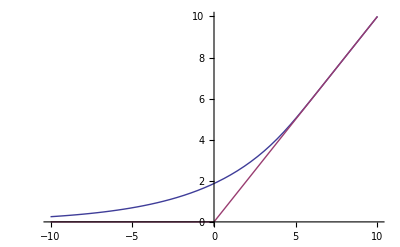

```mathematica
Plot[{PuttCSLA2[K,0, .5, .1], Max[K,0]},{K,-10,10}]
```

```mathematica
PutCSLAsigmaH[K_, S0_,   T_,sigma_, H_, alpha_]=FullSimplify[PutIntegral2[alpha  , sigma T^H, K-S0+SkewMean[ alpha , sigma T^H]]]
CallCSLAsigmaH[K_, S0_,   T_,sigma_, H_, alpha_]=(S0-K)+PutCSLAsigmaH[K, S0,   T,sigma, H, alpha]
```

sigma T^H Beta[1/(1+ⅇ^(((-K+S0) T^-H)/sigma-HarmonicNumber[-1+alpha])),alpha,0]

-K+S0+sigma T^H Beta[1/(1+ⅇ^(((-K+S0) T^-H)/sigma-HarmonicNumber[-1+alpha])),alpha,0]

```mathematica
CallCSLA2[.8, 1.2, 0.001, 0.005]
```

0.409958

Backtests

```mathematica
CallCSLAsigmaH[K, S0, T, sigma,   H, 1]
```

-K+S0-sigma T^H Log[1-1/(1+ⅇ^(((-K+S0) T^-H)/sigma))]

```mathematica
-K+S0-sigma T^H Log[1-1/(1+ⅇ^(((-K+S0) T^-H)/sigma))]
```

-K+S0-sigma T^H Log[1-1/(1+ⅇ^(((-K+S0) T^-H)/sigma))]

```mathematica
SSLACall[.8, 1.2, 1,  0.7,1]
```

0.713394

```mathematica
CallCSLAsigmaH[-1.1,- 2.1, 1, 1,1, 1]
SSLACall[-1.1,- 2.1,1,1,1]
```

0.313262

0.313262

```mathematica
CSLALNVolSurface[S0_,
sigma_,H_, alpha_]:=Module[{ Tmin, Tmax, Kstep, Kmax, Kmin, Nstrikes, Ntimes, Tstep },
Kmin=S0 0.8;
Kmax=S0 1.2;
Ntimes=15;
Nstrikes=15;
Kstep=(Kmax-Kmin)/(Nstrikes-1);
Tmin=0.5;
Tmax=2;
Tstep=(Tmax-Tmin)/(Ntimes-1);
Ktab=Table[Range[Kmin, Kmax, Kstep],{Nstrikes}];
Ttab=Transpose[Table[Range[Tmin, Tmax, Tstep],{Ntimes}]];


Prices= CallCSLAsigmaH[Ktab, S0, Ttab, sigma,  H, alpha] ;
Table[ImpliedVolLogNormal[S0,Ktab[[i,j]],Ttab[[i,j]], 0,  Prices[[i,j]] ], {j,Nstrikes}, {i,Ntimes}] 
]

CSLANVolSurface[S0_,
sigma_,H_, alpha_]:=Module[{ Tmin, Tmax, Kstep, Kmax, Kmin, Nstrikes, Ntimes, Tstep },
Kmin=S0 0.8;
Kmax=S0 1.2;
Ntimes=15;
Nstrikes=15;
Kstep=(Kmax-Kmin)/(Nstrikes-1);
Tmin=0.5;
Tmax=2;
Tstep=(Tmax-Tmin)/(Ntimes-1);
Ktab=Table[Range[Kmin, Kmax, Kstep],{Nstrikes}];
Ttab=Transpose[Table[Range[Tmin, Tmax, Tstep],{Ntimes}]];


Prices= CallCSLAsigmaH[Ktab, S0, Ttab, sigma,  H, alpha] ;
Table[ImpliedVolNormal[S0,Ktab[[i,j]],Ttab[[i,j]], 0,  Prices[[i,j]] ], {j,Nstrikes}, {i,Ntimes}] 
]
```

```mathematica
Timing[CSLALNVolSurface[1, 0.2,0.5, 1]]
Timing[SSLALNVolSurface[1, 0.2,0.5]]
```

{0.187,{{0.399726,0.398198,0.397185,0.396495,0.396018,0.395691,0.395474,0.395338,0.395266,0.395243,0.39526,0.39531,0.395386,0.395486,0.395604},{0.390276,0.389194,0.3885,0.388046,0.387752,0.38757,0.387468,0.387426,0.387432,0.387474,0.387546,0.387641,0.387757,0.38789,0.388036},{0.381557,0.380862,0.380441,0.38019,0.380051,0.379989,0.379984,0.380022,0.380092,0.380188,0.380304,0.380438,0.380585,0.380744,0.380913},{0.373555,0.373181,0.372986,0.3729,0.372887,0.372923,0.372997,0.373097,0.373219,0.373357,0.373508,0.37367,0.373842,0.374021,0.374207},{0.366254,0.366132,0.366112,0.366153,0.366236,0.366347,0.366479,0.366626,0.366786,0.366954,0.367131,0.367314,0.367502,0.367695,0.367891},{0.359637,0.359694,0.359796,0.359927,0.360075,0.360237,0.360408,0.360586,0.36077,0.360958,0.361149,0.361344,0.361542,0.361741,0.361943},{0.353684,0.353845,0.354017,0.354197,0.354382,0.35457,0.35476,0.354953,0.355148,0.355344,0.355542,0.35574,0.355939,0.35614,0.356341},{0.348371,0.348561,0.348751,0.348941,0.349132,0.349323,0.349515,0.349707,0.3499,0.350093,0.350286,0.35048,0.350675,0.35087,0.351065},{0.34367,0.343815,0.343972,0.344136,0.344304,0.344476,0.34465,0.344827,0.345005,0.345184,0.345365,0.345546,0.345729,0.345912,0.346096},{0.339547,0.33958,0.339655,0.339757,0.339875,0.340006,0.340146,0.340292,0.340443,0.340599,0.340758,0.340919,0.341083,0.341249,0.341417},{0.335967,0.335823,0.335773,0.335779,0.335823,0.335892,0.335981,0.336083,0.336197,0.336319,0.336448,0.336582,0.336721,0.336865,0.337011},{0.332888,0.332513,0.332297,0.332178,0.332123,0.332113,0.332135,0.332182,0.332247,0.332326,0.332417,0.332518,0.332627,0.332742,0.332863},{0.330269,0.329615,0.329198,0.328928,0.328754,0.328648,0.32859,0.328569,0.328576,0.328605,0.328651,0.328712,0.328785,0.328867,0.328958},{0.328067,0.327094,0.326448,0.326003,0.325692,0.325475,0.325326,0.325227,0.325167,0.325138,0.325133,0.325148,0.32518,0.325225,0.325282},{0.326238,0.324917,0.324017,0.323379,0.322916,0.322575,0.322323,0.322138,0.322004,0.32191,0.321848,0.321812,0.321799,0.321803,0.321823}}}

{0.204,{{0.399726,0.398198,0.397185,0.396495,0.396018,0.395691,0.395474,0.395338,0.395266,0.395243,0.39526,0.39531,0.395386,0.395486,0.395604},{0.390276,0.389194,0.3885,0.388046,0.387752,0.38757,0.387468,0.387426,0.387432,0.387474,0.387546,0.387641,0.387757,0.38789,0.388036},{0.381557,0.380862,0.380441,0.38019,0.380051,0.379989,0.379984,0.380022,0.380092,0.380188,0.380304,0.380438,0.380585,0.380744,0.380913},{0.373555,0.373181,0.372986,0.3729,0.372887,0.372923,0.372997,0.373097,0.373219,0.373357,0.373508,0.37367,0.373842,0.374021,0.374207},{0.366254,0.366132,0.366112,0.366153,0.366236,0.366347,0.366479,0.366626,0.366786,0.366954,0.367131,0.367314,0.367502,0.367695,0.367891},{0.359637,0.359694,0.359796,0.359927,0.360075,0.360237,0.360408,0.360586,0.36077,0.360958,0.361149,0.361344,0.361542,0.361741,0.361943},{0.353684,0.353845,0.354017,0.354197,0.354382,0.35457,0.35476,0.354953,0.355148,0.355344,0.355542,0.35574,0.355939,0.35614,0.356341},{0.348371,0.348561,0.348751,0.348941,0.349132,0.349323,0.349515,0.349707,0.3499,0.350093,0.350286,0.35048,0.350675,0.35087,0.351065},{0.34367,0.343815,0.343972,0.344136,0.344304,0.344476,0.34465,0.344827,0.345005,0.345184,0.345365,0.345546,0.345729,0.345912,0.346096},{0.339547,0.33958,0.339655,0.339757,0.339875,0.340006,0.340146,0.340292,0.340443,0.340599,0.340758,0.340919,0.341083,0.341249,0.341417},{0.335967,0.335823,0.335773,0.335779,0.335823,0.335892,0.335981,0.336083,0.336197,0.336319,0.336448,0.336582,0.336721,0.336865,0.337011},{0.332888,0.332513,0.332297,0.332178,0.332123,0.332113,0.332135,0.332182,0.332247,0.332326,0.332417,0.332518,0.332627,0.332742,0.332863},{0.330269,0.329615,0.329198,0.328928,0.328754,0.328648,0.32859,0.328569,0.328576,0.328605,0.328651,0.328712,0.328785,0.328867,0.328958},{0.328067,0.327094,0.326448,0.326003,0.325692,0.325475,0.325326,0.325227,0.325167,0.325138,0.325133,0.325148,0.32518,0.325225,0.325282},{0.326238,0.324917,0.324017,0.323379,0.322916,0.322575,0.322323,0.322138,0.322004,0.32191,0.321848,0.321812,0.321799,0.321803,0.321823}}}

```mathematica
Module[{S0},
S0=1;
Manipulate[ListPlot3D[CSLALNVolSurface[S0, sigma,H,alpha] , DataRange->{ {0.5, 2}, {S0 0.6, S0 1.4} }, PlotLabel->"CSLA Lornormal Volatility Surface"], {sigma, 0.1, 1}, {H, 0.1, 1},{alpha, 0.1,  10}]
Manipulate[ListPlot3D[CSLANVolSurface[S0, sigma,H,alpha] , DataRange->{ {0.5, 2}, {S0 0.6, S0 1.4} }, PlotLabel->"CSLA Normal Volatility Surface"], {sigma, 0.1, 1}, {H, 0.1, 1},{alpha, 0.1,  10}]

Manipulate[ListPlot3D[SSLALNVolSurface[S0, sigma,H] , DataRange->{ {0.5, 2}, {S0 0.6, S0 1.4} }, PlotLabel->"SSLA Lognormal Volatility Surface"], {sigma, 0.1, 1}, {H, 0.1, 1}
]]
```

```mathematica
Integral of the CDF of Log-Generalzied Logistic Type 4. Uses Hypergeometric represenatation eq (6) of Nassar Elmasry 2012. A put price exists! Martingale if s=alpha-beta
```

```mathematica
after logistic substitution thi is the				1 formula
```

```mathematica
Simplify[1/alpha/Beta[alpha,beta]Integrate[x^s/(1-x)^(s+1) Hypergeometric2F1[alpha,1-beta,1+alpha, x], x]]
```

(∫(1-x)^(-1-s) x^s Hypergeometric2F1[alpha,1-beta,1+alpha,x]ⅆx)/(alpha Beta[alpha,beta])

The formula above comes from representing 1F2 as a MEijer G, then using the subsitutiion y=1-z then applying either formulae in wikipedia

Implements sigma, H model for s

```mathematica
Simplify[Integrate[Exp[x (1+alpha/s)]/(1+Exp[x/s])^(alpha+beta), x]]
```

(ⅇ^(x+(alpha x)/s) s Hypergeometric2F1[alpha+beta,alpha+s,1+alpha+s,-ⅇ^(x/s)])/(alpha+s)

```mathematica
FullSimplify[D[(x/(1-x))^sigma,x]]
```

(sigma (x/(1-x))^sigma)/(x-x^2)

```mathematica
PutCPSLA[K_, S_,  c1_,c2_]=K BetaRegularized[  1/(1+(K/S)^(-1/(c2-c1))), c1,c2]-S BetaRegularized[  1/(1+(K/S)^(-1/(c2-c1))), c2,c1]
```

K BetaRegularized[1/(1+(K/S)^(-1/(-c1+c2))),c1,c2]-S BetaRegularized[1/(1+(K/S)^(-1/(-c1+c2))),c2,c1]

```mathematica
N[PutCPSLA[70.1, 31.4,  .5, 0.8]]
```

41.3513

```mathematica
CallCPSLA[K_, S_,  c1_,c2_]= S(1- BetaRegularized[  1/(1+(K/S)^(-1/(c2-c1))), c2,c1])-K(1- BetaRegularized[  1/(1+(K/S)^(-1/(c2-c1))), c1,c2])

CallCPSLA[3, 5,  0.6,1.4]
```

-K (1-BetaRegularized[1/(1+(K/S)^(-1/(-c1+c2))),c1,c2])+S (1-BetaRegularized[1/(1+(K/S)^(-1/(-c1+c2))),c2,c1])

3.21822

```mathematica
CallCPSLANew[K_, S_,  s_,b_]= S(BetaRegularized[  1/(1+(K/S)^(1/(b))), s,s+b])-K( BetaRegularized[  1/(1+(K/S)^(1/(b))), s+b,s])
```

S BetaRegularized[1/(1+(K/S)^(1/b)),s,b+s]-K BetaRegularized[1/(1+(K/S)^(1/b)),b+s,s]

```mathematica
CallCPSLANew[3, 5,  0.2,0.8]
```

4.01914

```mathematica
CallCPSLA2[3, 5,  0.6,0.8]
```

CallCPSLA2[3,5,0.6,0.8]

```mathematica
Manipulate[Plot[{PutCPSLA[K, 10,  c1, c2], Max[K-10,0]},{K,0,30}],{c2, 1, 2 }, {c1, 0,1}]
```

```mathematica
Manipulate[Plot[{CallCPSLA[K, 10,  c1, c2], Max[10-K,0]},{K,0,30}],{c2, 1, 2 }, {c1, 0,1}]
```

```mathematica
CallCPSLAsigmaH[K_, S_,T_, H_,  c1_,c2_]:=CallCPSLA[K, S,  c1 T^H,c2 T^H]




Manipulate[Plot[{CallCPSLAsigmaH[K, 10, T, H,  c1, c2], Max[10-K,0]},{K,0,30}],{c2, 1, 2 }, {c1, 0,1},{H,0.1,2 },{T,0.01, 5}]
```

```mathematica
CallCPDAsigmaH[K_, S_,T_, sigma_,H_, c2_]:=CallCPSLA[K, S,  c2(1-b[T, sigma, H]),c2]
```

Backtest to CPDA

```mathematica
CPDACall[.3, 1.2, 1.6, 0.12,0.35]
CallCPDAsigmaH[.3, 1.2, 1.6, 0.12,0.35,1]
```

0.900009

0.900009

```mathematica
CPSLALNVolSurface[S0_,sigma_, H_, c2_ ]:=Module[{ Tmin, Tmax, Kstep, Kmax, Kmin, Nstrikes, Ntimes, Tstep },
Kmin=S0 0.6;
Kmax=S0 1.4;
Ntimes=15;
Nstrikes=15;
Kstep=(Kmax-Kmin)/(Nstrikes-1);
Tmin=0.5;
Tmax=2;
Tstep=(Tmax-Tmin)/(Ntimes-1);
Ktab=Table[Range[Kmin, Kmax, Kstep],{Ntimes}];
Ttab=Transpose[Table[Range[Tmin, Tmax, Tstep],{Nstrikes}]];
Prices= CallCPDAsigmaH[Ktab, S0,Ttab, sigma,H, c2]; 
Table[ImpliedVolLogNormal[S0,Ktab[[i,j]],Ttab[[i,j]], 0,  Prices[[i,j]] ], {j,Nstrikes}, {i,Ntimes}] 
]
```

```mathematica
Timing[CPSLALNVolSurface[1, 0.5,0.25, 1]]
```

{0.203,{{1.25481,1.20585,1.1671,1.13533,1.10861,1.08567,1.06569,1.04804,1.03231,1.01814,1.0053,0.993581,0.982825,0.972903,0.96371},{1.2476,1.19955,1.16147,1.13022,1.10391,1.08132,1.06162,1.04422,1.0287,1.01472,1.00204,0.990468,0.979842,0.970037,0.960952},{1.24209,1.19474,1.15718,1.12634,1.10035,1.07802,1.05854,1.04133,1.02597,1.01213,0.999578,0.988115,0.977588,0.967874,0.95887},{1.23801,1.19119,1.15401,1.12347,1.09772,1.07559,1.05627,1.0392,1.02396,1.01023,0.997767,0.986386,0.975933,0.966284,0.95734},{1.23512,1.18867,1.15178,1.12145,1.09587,1.07388,1.05468,1.0377,1.02255,1.00889,0.996493,0.98517,0.974769,0.965168,0.956266},{1.23324,1.18704,1.15033,1.12013,1.09466,1.07276,1.05364,1.03673,1.02163,1.00802,0.995667,0.984382,0.974014,0.964444,0.95557},{1.2322,1.18614,1.14953,1.11941,1.094,1.07215,1.05307,1.0362,1.02113,1.00754,0.995214,0.98395,0.973601,0.964047,0.955189},{1.23189,1.18587,1.14928,1.11919,1.0938,1.07196,1.05289,1.03603,1.02097,1.0074,0.995075,0.983817,0.973474,0.963925,0.955071},{1.23217,1.18611,1.1495,1.11939,1.09398,1.07213,1.05305,1.03618,1.02111,1.00753,0.995199,0.983935,0.973587,0.964034,0.955176},{1.23296,1.1868,1.15011,1.11994,1.09449,1.0726,1.05349,1.03659,1.02149,1.00789,0.995545,0.984266,0.973904,0.964338,0.955468},{1.23418,1.18786,1.15105,1.12079,1.09526,1.07332,1.05416,1.03722,1.02209,1.00845,0.99608,0.984776,0.974392,0.964806,0.955918},{1.23575,1.18923,1.15227,1.12189,1.09627,1.07425,1.05503,1.03803,1.02286,1.00918,0.996773,0.985437,0.975025,0.965413,0.956502},{1.23763,1.19086,1.15372,1.1232,1.09748,1.07537,1.05606,1.03901,1.02377,1.01005,0.9976,0.986227,0.975781,0.966139,0.9572},{1.23976,1.19271,1.15537,1.1247,1.09884,1.07663,1.05724,1.04011,1.02482,1.01104,0.998541,0.987125,0.976641,0.966964,0.957994},{1.24209,1.19474,1.15718,1.12634,1.10035,1.07802,1.05854,1.04133,1.02597,1.01213,0.999578,0.988115,0.977588,0.967874,0.95887}}}

```mathematica
Timing[CPDAVolSurface[1, 0.5,0.25]]
```

{0.188,{{1.25481,1.20585,1.1671,1.13533,1.10861,1.08567,1.06569,1.04804,1.03231,1.01814,1.0053,0.993581,0.982825,0.972903,0.96371},{1.2476,1.19955,1.16147,1.13022,1.10391,1.08132,1.06162,1.04422,1.0287,1.01472,1.00204,0.990468,0.979842,0.970037,0.960952},{1.24209,1.19474,1.15718,1.12634,1.10035,1.07802,1.05854,1.04133,1.02597,1.01213,0.999578,0.988115,0.977588,0.967874,0.95887},{1.23801,1.19119,1.15401,1.12347,1.09772,1.07559,1.05627,1.0392,1.02396,1.01023,0.997767,0.986386,0.975933,0.966284,0.95734},{1.23512,1.18867,1.15178,1.12145,1.09587,1.07388,1.05468,1.0377,1.02255,1.00889,0.996493,0.98517,0.974769,0.965168,0.956266},{1.23324,1.18704,1.15033,1.12013,1.09466,1.07276,1.05364,1.03673,1.02163,1.00802,0.995667,0.984382,0.974014,0.964444,0.95557},{1.2322,1.18614,1.14953,1.11941,1.094,1.07215,1.05307,1.0362,1.02113,1.00754,0.995214,0.98395,0.973601,0.964047,0.955189},{1.23189,1.18587,1.14928,1.11919,1.0938,1.07196,1.05289,1.03603,1.02097,1.0074,0.995075,0.983817,0.973474,0.963925,0.955071},{1.23217,1.18611,1.1495,1.11939,1.09398,1.07213,1.05305,1.03618,1.02111,1.00753,0.995199,0.983935,0.973587,0.964034,0.955176},{1.23296,1.1868,1.15011,1.11994,1.09449,1.0726,1.05349,1.03659,1.02149,1.00789,0.995545,0.984266,0.973904,0.964338,0.955468},{1.23418,1.18786,1.15105,1.12079,1.09526,1.07332,1.05416,1.03722,1.02209,1.00845,0.99608,0.984776,0.974392,0.964806,0.955918},{1.23575,1.18923,1.15227,1.12189,1.09627,1.07425,1.05503,1.03803,1.02286,1.00918,0.996773,0.985437,0.975025,0.965413,0.956502},{1.23763,1.19086,1.15372,1.1232,1.09748,1.07537,1.05606,1.03901,1.02377,1.01005,0.9976,0.986227,0.975781,0.966139,0.9572},{1.23976,1.19271,1.15537,1.1247,1.09884,1.07663,1.05724,1.04011,1.02482,1.01104,0.998541,0.987125,0.976641,0.966964,0.957994},{1.24209,1.19474,1.15718,1.12634,1.10035,1.07802,1.05854,1.04133,1.02597,1.01213,0.999578,0.988115,0.977588,0.967874,0.95887}}}

```mathematica
Module[{S0},
S0=1;
Manipulate[ListPlot3D[CPSLALNVolSurface[S0, sigma, H, c2] , DataRange->{ {0.5, 2}, {S0 0.6, S0 1.4} }, PlotLabel->"CPSLA Volatility Surface"], {sigma, 0.1, 1}, {H, 0.1, 1},{c2, 
.01,  2}]
Manipulate[ListPlot3D[CPDAVolSurface[S0, sigma, H] , DataRange->{ {0.5, 2}, {S0 0.6, S0 1.4} }, PlotLabel->"CPDA Volatility Surface"], {sigma, 0.1, 1}, {H, 0.1, 1}
]
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: "lstol" will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: "lstol" will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: "lstol" will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: "lstol" will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: "lstol" will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: "lstol" will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: "lstol" will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: "lstol" will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: "lstol" will be suppressed during this calculation.

FindRoot::nlnum: The function value {1.\ S0$3000708 - 1.00005\ (S0$3000708^14.1598)^0.0706224} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.5, 0] == -0.6\ S0$3000708 + 1.00005\ (S0$3000708^14.1598)^0.0706224, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {1.00002\ S0$3000708 - 1.00011\ (S0$3000708^12.8533)^0.0778013} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.607143, 0] == -0.6\ S0$3000708 + 1.00011\ (S0$3000708^12.8533)^0.0778013, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {1.00005\ S0$3000708 - 1.0002\ (S0$3000708^11.8533)^0.0843647} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

General::stop: Further output of FindRoot :: "nlnum" will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.714286, 0] == -0.6\ S0$3000708 + 1.0002\ (S0$3000708^11.8533)^0.0843647, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

DataRange::invdrange: {{0.5, 2.}, {0.6\ S0$3000708, 1.4\ S0$3000708}} must be of the form {xmin, xmax}.

FindRoot::nlnum: The function value {-0.0000231293\ S0$3000708} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.5, 0] == 0.400027\ S0$3000708, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.0000419521\ S0$3000708} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.607143, 0] == 0.400059\ S0$3000708, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.0000601405\ S0$3000708} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

General::stop: Further output of FindRoot :: "nlnum" will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.714286, 0] == 0.400106\ S0$3000708, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

DataRange::invdrange: {{0.5, 2.}, {0.6\ S0$3000708, 1.4\ S0$3000708}} must be of the form {xmin, xmax}.

FindRoot::nlnum: The function value {1.\ S0$3000708 - 1.00005\ (S0$3000708^14.1598)^0.0706224} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.5, 0] == -0.6\ S0$3000708 + 1.00005\ (S0$3000708^14.1598)^0.0706224, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {1.00002\ S0$3000708 - 1.00011\ (S0$3000708^12.8533)^0.0778013} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.607143, 0] == -0.6\ S0$3000708 + 1.00011\ (S0$3000708^12.8533)^0.0778013, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {1.00005\ S0$3000708 - 1.0002\ (S0$3000708^11.8533)^0.0843647} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

General::stop: Further output of FindRoot :: "nlnum" will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.714286, 0] == -0.6\ S0$3000708 + 1.0002\ (S0$3000708^11.8533)^0.0843647, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

DataRange::invdrange: {{0.5, 2.}, {0.6\ S0$3000708, 1.4\ S0$3000708}} must be of the form {xmin, xmax}.

FindRoot::nlnum: The function value {-0.0000231293\ S0$3000708} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.5, 0] == 0.400027\ S0$3000708, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.0000419521\ S0$3000708} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.607143, 0] == 0.400059\ S0$3000708, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.0000601405\ S0$3000708} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

General::stop: Further output of FindRoot :: "nlnum" will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.714286, 0] == 0.400106\ S0$3000708, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

DataRange::invdrange: {{0.5, 2.}, {0.6\ S0$3000708, 1.4\ S0$3000708}} must be of the form {xmin, xmax}.

FindRoot::nlnum: The function value {1.\ S0$3000708 - 1.00005\ (S0$3000708^14.1598)^0.0706224} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.5, 0] == -0.6\ S0$3000708 + 1.00005\ (S0$3000708^14.1598)^0.0706224, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {1.00002\ S0$3000708 - 1.00011\ (S0$3000708^12.8533)^0.0778013} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.607143, 0] == -0.6\ S0$3000708 + 1.00011\ (S0$3000708^12.8533)^0.0778013, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {1.00005\ S0$3000708 - 1.0002\ (S0$3000708^11.8533)^0.0843647} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

General::stop: Further output of FindRoot :: "nlnum" will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.714286, 0] == -0.6\ S0$3000708 + 1.0002\ (S0$3000708^11.8533)^0.0843647, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

DataRange::invdrange: {{0.5, 2.}, {0.6\ S0$3000708, 1.4\ S0$3000708}} must be of the form {xmin, xmax}.

FindRoot::nlnum: The function value {-0.0000231293\ S0$3000708} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.5, 0] == 0.400027\ S0$3000708, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.0000419521\ S0$3000708} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.607143, 0] == 0.400059\ S0$3000708, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.0000601405\ S0$3000708} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

General::stop: Further output of FindRoot :: "nlnum" will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$3000708, 0.6\ S0$3000708, sigma, 0.714286, 0] == 0.400106\ S0$3000708, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

DataRange::invdrange: {{0.5, 2.}, {0.6\ S0$3000708, 1.4\ S0$3000708}} must be of the form {xmin, xmax}.

DataRange::invdrange: {{0.5, 2.}, {0.6\ S0$2333594, 1.4\ S0$2333594}} must be of the form {xmin, xmax}.

ListPlot3D::arrayerr: CPDAVolSurface[S0$2333594, 0.3, 0.5] must be a valid array or a list of valid arrays.

DataRange::invdrange: {{0.5, 2.}, {0.6\ S0$2333594, 1.4\ S0$2333594}} must be of the form {xmin, xmax}.

ListPlot3D::arrayerr: CPSLALNVolSurface[S0$2333594, 0.3, 0.5, 0.1] must be a valid array or a list of valid arrays.

DataRange::invdrange: {{0.5, 2.}, {0.6\ S0$2333594, 1.4\ S0$2333594}} must be of the form {xmin, xmax}.

ListPlot3D::arrayerr: CPDAVolSurface[S0$2333594, 0.3, 0.5] must be a valid array or a list of valid arrays.

DataRange::invdrange: {{0.5, 2.}, {0.6\ S0$2333594, 1.4\ S0$2333594}} must be of the form {xmin, xmax}.

ListPlot3D::arrayerr: CPSLALNVolSurface[S0$2333594, 0.3, 0.5, 0.1] must be a valid array or a list of valid arrays.

FindRoot::nlnum: The function value {1.\ S0$2333594 - 1.01777\ (S0$2333594^4.76718)^0.209768} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$2333594, 0.6\ S0$2333594, sigma, 0.5, 0] == -0.6\ S0$2333594 + 1.01777\ (S0$2333594^4.76718)^0.209768, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {1.00002\ S0$2333594 - 1.02417\ (S0$2333594^4.3365)^0.230601} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$2333594, 0.6\ S0$2333594, sigma, 0.607143, 0] == -0.6\ S0$2333594 + 1.02417\ (S0$2333594^4.3365)^0.230601, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {1.00005\ S0$2333594 - 1.03076\ (S0$2333594^4.00761)^0.249525} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

General::stop: Further output of FindRoot :: "nlnum" will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$2333594, 0.6\ S0$2333594, sigma, 0.714286, 0] == -0.6\ S0$2333594 + 1.03076\ (S0$2333594^4.00761)^0.249525, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

DataRange::invdrange: {{0.5, 2.}, {0.6\ S0$2333594, 1.4\ S0$2333594}} must be of the form {xmin, xmax}.

FindRoot::nlnum: The function value {-0.0103768\ S0$2333594} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$2333594, 0.6\ S0$2333594, sigma, 0.5, 0] == 0.410381\ S0$2333594, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.0143667\ S0$2333594} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$2333594, 0.6\ S0$2333594, sigma, 0.607143, 0] == 0.414383\ S0$2333594, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.0185591\ S0$2333594} is not a list of numbers with dimensions {1} at {sigma} = {0.2}.

General::stop: Further output of FindRoot :: "nlnum" will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[BlackScholesCall[S0$2333594, 0.6\ S0$2333594, sigma, 0.714286, 0] == 0.418605\ S0$2333594, {sigma, 0.2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

DataRange::invdrange: {{0.5, 2.}, {0.6\ S0$2333594, 1.4\ S0$2333594}} must be of the form {xmin, xmax}.